```mathematica
cols=Short[ColorData[109,"ColorList"],4];
col1=cols[[1,8]]
col2=cols⟦1,9⟧
col3=cols[[1,10]]
col4=cols[[1,7]]
```

RGBColor[1., 0.325204, 0.406504]

RGBColor[0., 0.786874, 0.739379]

RGBColor[1., 0.520437, 0.]

RGBColor[0.238758, 0.610466, 1.]

```mathematica
(*---------------Funtions for normal---------------*)
δn[p_,q_]:=Subscript[δ, min]+(Subscript[δ, 0]-Subscript[δ, min])*Exp[-(p-q)^2/(2*Subscript[k, 1]^2)];
ρn[p_]:=Subscript[ρ, min]+(Subscript[ρ, 0]-Subscript[ρ, min])*Exp[-p^2/(2*Subscript[k, 2]^2)];
μn[q_]:=Subscript[μ, min]+(Subscript[μ, 0]-Subscript[μ, min])*Exp[-q^2/(2*Subscript[k, 3]^2)];
G1n[ϕ1_,p_,q_,u_,v_]:=ρn[ϕ1]*(1-u/κ)-(δn[ϕ1,q]*v)/(1+δn[ϕ1,q]*γ*u);
G2n[ϕ2_,p_,q_,u_,v_]:=(α*δn[p,ϕ2]*u)/(1+δn[p,ϕ2]*γ*u)-μn[ϕ2];
G11n[p_,q_,u_,v_]:=D[G1n[ϕ1,p,q,u,v],{ϕ1,1} ] /.ϕ1->p;
G22n[p_,q_,u_,v_]:=D[G2n[ϕ2,p,q,u,v],{ϕ2,1} ] /.ϕ2->q;
```

```mathematica
(*------------------Funtions for trade off--------------------*)
δ[p_,q_]:=Subscript[δ, min]+(Subscript[δ, 0]-Subscript[δ, min])/(1+Exp[Subscript[k, 4]*(p-q)]);
ρ[p_]:=Subscript[ρ, min]+(Subscript[ρ, 0]-Subscript[ρ, min])/(1+Exp[Subscript[k, 5]*p]);
μ[q_]:=Subscript[μ, min]+(Subscript[μ, 0]-Subscript[μ, min])/(1+Exp[-Subscript[k, 6]*q]);
G1[ϕ1_,p_,q_,u_,v_]:=ρ[ϕ1]*(1-u/κ)-(δ[ϕ1,q]*v)/(1+δ[ϕ1,q]*γ*u);
G2[ϕ2_,p_,q_,u_,v_]:=(α*δ[p,ϕ2]*u)/(1+δ[p,ϕ2]*γ*u)-μ[ϕ2];
G11[p_,q_,u_,v_]:=D[G1[ϕ1,p,q,u,v],{ϕ1,1} ] /.ϕ1->p;
G22[p_,q_,u_,v_]:=D[G2[ϕ2,p,q,u,v],{ϕ2,1} ] /.ϕ2->q;
```

```mathematica
Subscript[ρ, 0]=0.5;Subscript[ρ, min]=0.25;κ=150;Subscript[δ, 0]=0.15;Subscript[δ, min]=0.05;γ=0.1;α=0.7;Subscript[μ, 0]=2.0;Subscript[μ, min]=1.0;Subscript[k, 1]=0.5;Subscript[k, 2]=0.5;Subscript[k, 3]=0.5;Subscript[k, 4]=1;
Subscript[k, 5]=0.1;
Subscript[k, 6]=1;
f=0.5;
(*---------------------------------numetrical solution logistic normal------------------------------------*)
sol1=NDSolve[{u'[t]==u[t]*G1n[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11n[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2n[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22n[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];

(*---------------------------------numetrical solution logistic trade off------------------------------------*)
sol3=NDSolve[{u'[t]==u[t]*G1[p[t],p[t],q[t],u[t],v[t]],p'[t]==f*G11[p[t],q[t],u[t],v[t]],v'[t]==v[t]*G2[q[t],p[t],q[t],u[t],v[t]],q'[t]==f*G22[p[t],q[t],u[t],v[t]],u[0]==3,p[0]==2,v[0]==3,q[0]==-2},{u,p,v,q},{t,0,10000},AccuracyGoal->8,PrecisionGoal->6,MaxSteps->10^6];
```

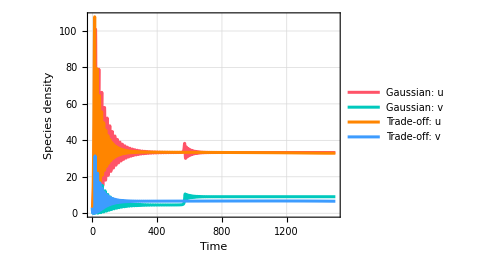
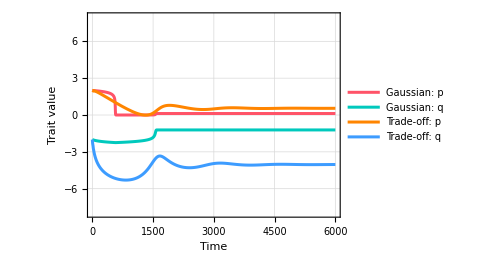
A | B
-Graphics- | -Graphics-

```mathematica
(*---fig 4A:Species densities---*)
A11=Plot[Evaluate[{u[t]/. sol1,v[t]/. sol1,u[t]/. sol3,v[t]/. sol3}],{t,0,1500},PlotRange->{All,All},PlotLegends->Placed[{"Gaussian: u","Gaussian: v","Trade-off: u","Trade-off: v"},{0.8,0.75}],LabelStyle->{FontSize->14},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Time","Species density"},PlotStyle->{{col1,Thickness[0.006]},{col2,Thickness[0.006]},{col3,Thickness[0.006]},{col4,Thickness[0.006]}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],AspectRatio->1.5/2.1,ImageSize->Medium];
(*---fig 4A:Species densities---*)
A12=Plot[Evaluate[{p[t]/. sol1,q[t]/. sol1,p[t]/. sol3,q[t]/. sol3}],{t,0,6000},PlotRange->{All,{-8,8}},PlotLegends->Placed[{"Gaussian: p","Gaussian: q","Trade-off: p","Trade-off: q"},{0.8,0.75}],LabelStyle->{FontSize->14},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Time","Trait value"},PlotStyle->{{col1,Thickness[0.006]},{col2,Thickness[0.006]},{col3,Thickness[0.006]},{col4,Thickness[0.006]}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.5],Dotted,Thickness[0.002]],AspectRatio->1.5/2.1,ImageSize->Medium];
g=Grid[{{Style["A",20],Style["B",20]},{A11,A12}}]
```

```mathematica
Export[SystemDialogInput["FileSave","enrich2.pdf"],g,ImageResolution->350,"CompressionLevel"->0]
```

C:\Users\SANTANA\Dropbox\SANTANA\P7_G function\Mondal_allee effect\enrich2.pdf

```mathematica
g
```

g